# The eCF-Project—Final Report

Wolfram Foundation, October 2013

PI: Michael Trott
co-PI: Eric Weisstein
Oleg Marichev, Todd Rowland

## Introduction

The entire world's mathematical knowledge is contained in about 100 million pages of mathematical articles and books. Contrary to all other sciences, mathematical knowledge does not age, and consequently, mathematical results found 100 or even 200 years ago are still of relevance today.

The International Mathematical Union and the US National Research Council are currently evaluating the possibility and potential form of a future World Heritage Digital Mathematics Library. Existing digital mathematics libraries like the European Digital Mathematics Library currently only collect older mathematical articles and books. A future digital mathematical library should index pure mathematical content including theorems, mathematical identities, and definitions from the original literature without requiring the user to read through the original papers or books.

## Summary

The overall goal of the eCF project was to prototype potential features of a mathematical digital library with the additional goal of increasing the accessibility of a chosen segment of mathematical knowledge: the theory of continued fractions.

The project was carried out from March 2012 to September 2013 by Oleg Marichev, Todd Rowland, Michael Trott, and Eric Weisstein from Wolfram|Alpha with partial support from summer intern Chris Stover, a graduate student from Florida State University.

The project required making results about continued fractions from mathematical literature easier and faster to find, retrieve, understand, embed in context, and use. The intended audience included both mathematicians and non-mathematicians, including engineers and physicists, that use continued fractions in their work and are interested in various properties of continued fractions.

Because non-mathematicians are primarily interested in mathematical results and not the original publications in which they first appeared, we extracted results from original works via digitization, linking, classifaction, and review. In contrast to previous efforts to build digital mathematical libraries, this made it possible to focus on theorems and results, recategorize them by their governing mathematics, and display them in standalone form.

In the course of our research, we primarily mined papers from the GDZ and JSTOR archives, but we also included results from books and newer research literature. We used this cross section of old and new literature to test the viability of our approach, as publications from different times show a broad spectrum of notations, languages, degrees of abstraction and generality, interrelations to previous results, and forms of presentation. For each of the selected publications, we extracted and verified theorems and other results and encoded them syntactically, semantically, and in some cases computationally. In addition, we added mathematical keyword tagging to the extracted information and linked it to the author, publication name, and other bibliographical data.

The advantage of a semantic representation is that the resulting entities can be linked to other mathematical and non-mathematical data, programmatically searched, reassembled, and re-exposed in a variety of ways. An added bonus of hand-curation is the canonicalization and uniformization of variable names, notation, and terminology. The process greatly aided in the understanding of a result or group of results originating from different sources whose notational mixture of a, b, A, B, p, q, P, Q, a(n), a_n, etc. for partial denominators, convergents, and so forth, could otherwise be a source of confusion. In particular, older literature uses notations that are difficult to read and sometimes ambiguous. Here is a typical example from the central result of Glaisher’s paper from 1874 (alpha(Glaisher’s 1874 work)) about the connection of certain products and continued fractions:

-Graphics-

In modern notation and for formal use, it is essential to use an indexed notation such as alpha instead of ellipsis to convert a product into a continued fraction. Although the meaning of Glaisher’s notation can be deduced after some thought, any structure with explicit ellipsis is de-facto unusable in a computational manner.

Theorems from non-English sources were translated into English. Furthermore, to make the individual blocks of mathematical knowledge maximally useful, we presented them in self-contained form wherever possible. In the existing literature, however, a theorem often refers to notations introduced earlier in a publication and is not self-contained.

Unlike a traditional, printed library, a digital library allowed us to add new features. We concentrated on the following three elements, adding qualitative new features not availabe from traditional libraries: natural language search, extemporaneous calculations, and interlinked results.

Fixed, pre-generated indexes used in traditional libraries are limiting. With a digital library, users can access material in a variety of ways. The most natural, convenient and powerful approach is using natural language. Building on the Wolfram|Alpha infrastructure, we indexed eCF project material using the natural language interface of Wolfram|Alpha.

A printed treatment of continued fractions often contains various author-chosen examples. In a digital library the user can provide inputs so that visualizations and algorithm steps can be calculated extemporaneously, allowing for a much richer and more insightful user experience. In our case, this was made possible by using Mathematica, the computational engine powering Wolfram|Alpha. It provided a large amount of mathematical infrastructure (e.g., an understanding of quantifiers and mathematical functions) which allowed, for instance, checking the applicability of the encoded information to a given mathematical expression and providing interactive visualizations for user-chosen inputs.

In a digital library, it is possible to interlink results. Within our structure, theorems, bibliographic sources, and continued fraction identities are interlinked canonical entities that have a variety of properties attached. Naturally, we also linked the mathematical results to the papers from which they originated. As the links often refer themselves to entities (e.g., authors), we can enrich the information by linking to additional resources of relevance (e.g., data about the authors).

The goal of building a digital mathematics library was not to be a monograph surveying the field of continued fractions or a textbook introducing the field, but rather to be a condensed core mathematical summary of the published literature at the level of the individual identities, formulas, and theorems. To be truly useful, the digital library required a certain amount of completion of previously published work. To demonstrate this, we derived various new results to round up existing tables of identities. We not only encoded core results from selected mathematical papers, but also from some books (e.g., Oskar Perron's classic two-volume Die Lehre von den Kettenbrüchen from 1913) to cover a certain amount of general knowledge about continued fractions.

The key features of our implementation of the continued fraction digital library are:

Contains human- and computer-verified formulas, identities, and theorems

Stored in computer-readable (and, if suitable, computational) form

Searchable using a natural language interface

Linked to the original literature

Presented in a coherent, unified, and verified form using consistent notation and integrated definitions

Interlinked in a way that reflects the rich connections and interdependence of mathematical results

Reflects the mathematical heritage literature and being independent of current research trends

Easily and freely accessible to everyone at all times

The prototype implementation of facets of our vision of a digital mathematics library was not intended to cover the field exhaustively, but rather to identify the best features of a twenty-first century digital mathematics library: easy searchability through natural language; concise, self-contained, interlinked search results; and advanced computational visualizations and demonstrations made possible by modern-day computing and natural language processing technologies.

## Digital Library: Content and Implementation

The field of continued fractions dates back to Euclid, and it became popular in the sixteenth century with the works of Bombelli and Cataldi. A fair fraction of results was produced in the eighteenth and nineteenth century starting with the numerous works of Euler. While there are still publications about new results for continued fractions today, it is no longer a mainstream field of modern mathematics. However, its classical results are still of great importance and use.

In our prototype implementation, we focused on extracting five main types of mathematical knowledge: (1) definitions and concepts related to continued fractions; (2) concrete mathematical formulas about continued fractions; (3) theorems, conjectures, and corollaries about continued fractions; (4) algorithms about continued fractions; and (5) the mathematical references from which the material for categories one through four was extracted.

These five categories cover a large portion of the mathematics of continued fractions. The difference between categories two, three, and four are more historical and less mathematical. An algorithm can be viewed as a constructive theorem as well as a concrete mathematical formula. Formulas are often collected in formula tables, and theorems are typically not published as collections. To better represent standard conventions, we used different approaches and implementations for each category.

While the field of continued fractions is just a subfield of all mathematics, it still contains more than 100,000 pages of published literature. This was too much to deal with exhaustively within our prototype implementation. However, to test the applicability of our approach, we selected some specific topics and aimed for comprehensive coverage of all knowledge known about certain types of continued fractions. The two topics where we aimed for an exhaustive treatment were: (1) explicit continued fraction expansions for mathematical constants and functions; and (2) special cases, modular equations, and companion equations of the Rogers-Ramanujan continued fraction. (There are only a few named continued fractions, but by far the most popular one is the Rogers-Ramanujan continued fraction, which made this fraction a natural choice.)

At the software implementation level, we loosely followed a four-category ontology. Every main mathematical fact (e.g., a mathematical identity or a theorem) is an entity and it has properties (e.g., who proved it, when was it proved, in which publication the proof was published, under which conditions it holds, and which mathematical concepts are associated with it). In connection with other Wolfram|Alpha knowledge bases (e.g., about people), we can provide rich and informative result pages. For instance, the query for “who proved the Stern-Stolz theorem” does not just return the names of both people, but also shows basic information for Moritz Stern and Otto Stolz including birthdates, birthplaces, and images.

In the following sections, we briefly describe approaches and content for all five knowledge categories and supply a representative set of sample queries that Wolfram|Alpha can answer using the data from the eCF project.

### Definitions and concepts related to continued fractions

An integral part of any library covering a specific subject is defining the terms used within the field. Therefore, we included about 40 definitions related to continued fractions.

In addition to definitions, we also created a list of about 45 concepts including terms like "convergents," "continuant," or "singularization." These concepts proved to be quite useful. Mathematical papers are classified according to the Mathematics Subject Classification 2010 (http://www.ams.org/mathscinet/msc/msc2010.html) for precisely referring to individual theorems. However, in practice users need much more specific terminology, and most of the concept names we used do not occur in the MSC 2010. Our concepts allow users to zero in on the most relevant theorems.

Jim Pitman at UC Berkeley recently emphasized the importance of what he called a mathematical wordnet. Our list of concepts is a realization of his idea specific to the topic of continued fractions.

#### Sample queries for definitions and concepts

Basic definitions

common notations for continued fractions

what is a regular continued fraction

definition of a finite regular continued fraction

the even part of a continued fraction

recurrence relations for continued fraction convergents

what’s divergence of a regular continued fraction

even contraction of a continued fraction

formal numerator

what’s a best left approximation

information about the Lyapunov exponent of the Gauss map

continued fraction solution of the generalized Riccati differential equation

Definitions of concepts

Gauss map for continued fractions

chordal metric on the Riemann sphere

dually regular chain

show the Gauss-Kuzmin-Wirsing operator

improper unimodular map

what does properly equivalent mean

what’s a branched continued fraction

omg, what’s approximations in defect

higher-order Khinchin constants

C-dual convergents

continued fractions equivalence transformations

equivalent continued fraction with unit denominators

tell me about iterated linear fractional transformations

continued fraction singularization

Bauer-Muir continued fraction transformation

tell me about higher-order Khinchin constants

what are multidimensional continued fractions

three term recurrence minimal solution

Definitions of continued fraction types

what is a Thron fraction?

what is a modified Stieltjes fraction?

T-fractions versus J-fractions vs M-fraction vs P-fraction vs S-fraction

tell me about alpha-Rosen continued fractions

lambda_q-fractions

loxodromic continued fraction

Perron-Caratheodory continued fractions

Rudin-Shapiro continued fraction versus Schur-Nevanlinna continued fraction

tau cf, T cf, thiele fraction, thron fraction

information about Baum-Sweet continued fractions

### Concrete mathematical formulas about continued fractions

#### Mathematical identities for continued fractions

There are only a handful of common generic operations in mathematics that apply to arbitrary functions and have their own symbol: differentiation ∂, integration ∫, summation ∑, products Π, and continued fraction expansions K. Differentiation can be carried out algorithmically using a few simple rules. The classical handbooks of integrals and sums (e.g.,  I. S. Gradshteyn, I. M. Ryzhik: Table of Integrals, Series and Products; E. R. Hansen: A Table of Series and Products; and A. P. Prudnikov, Yu. A. Brychkov and O. I. Marichev: Integrals and Series) have helped generations of mathematicians and scientists do their integrals, sums, and products. Today, however, it is more and more common for integrals and sums to be calculated by computational software rather than by hand. Remarkably, there is no handbook of continued fractions available. Mathematical handbooks and formula collections started to become popular by the end of the nineteenth century, but no table was ever made for continued fractions. As concrete continued fraction expansions of a given mathematical function are useful for a variety of applications (e.g., for various perturbation expansions in quantum mechanics), we created a complete table of all continued fraction expansions from the literature.

Typical examples are:

π=3+K_(k=1)^∞(2 k-1)^2/6

((a b+d) e/d(a b+d)/a^2d/a^2)/(a 1+e/d1+(a b+d)/a^2d/a^2)-b==K_(k=1)^∞(d k+e)/(a k+b)

ⅇ^z 0z==1/(z+K_(k=1)^∞Floor[(k+1)/2]/(1/2 ((-1)^k z-(-1)^k+z+1)))

To make these tables useful today, a large fraction of these identities had to be adapted for modern conventions, especially branch cuts of elementary functions. Frequently in older literature, and sometimes in modern literature as well, identities are given in forms that are only correct on a part of the real axis. The reason being that in a paper-and-pencil calculation one can choose branch cuts as needed, but in computational software branch cuts are fixed by the IEEE 754 standard. By properly rewriting the identities, one can make them correct in the whole complex plane. In these forms, the identities are much more useful, especially in computational software. The next formula shows the simplest possible case (alpha(constant/constant continued fraction identities)):

K_(k=1)^∞a/b=(2 a)/(b+√(4 a+b^2))  ⟹  K_(k=1)^∞a/b=(2 a)/(b (1+√((4 a)/b^2+1)))

The left identity (found in the literature) is incorrect for a=2,b=-2, while the right identity is correct for all complex a and b.

The table compiled contains about 1,460 base cases of continued fractions. About two-thirds of these identities appear in the literature explicitly; the remaining third are not explicit in the literature but implicit, e.g., in the form of relations between continued fractions and infinite series. All identities were verified, various typographical errors and mistakes from the literature were corrected, and the identities were made correct as much as possible for complex arguments.

Each continued fraction occurs in a variety of forms, the so-called equivalent continued fractions. Our tables contain another 12,200 of such continued fractions. For comparison, the 1,160-page Gradshteyn-Ryzhik book contains about 5,800 integrals; so our collection represents the first ever comprehensive continued fraction expansion of functions that, when printed, would fill a 1,200 page book.

In addition to expanding an expression into a continued fraction, sometimes it is necessary to calculate the closed form of a continued fraction. We also created the first complete table of this kind. For example the so-called Nörlund's formula as found in the literature is

abcz/(a+1b+1c+1z)==1-(z (a+b+1))/c+1/c K_(k=1)^∞((a+k) (b+k)(z-z^2))/(c+k-z (a+b+2 k+1)),

but rewritten in the form (alpha(quadratic/linear continued fraction identities)) it is substantially more useful:

K_(k=1)^∞(c k^2+d k+e)/(a k+b)=(√(a^2+4 c) (c+d)-a (c+d)+2 b c)((d-√(d^2-4 c e))/(2 c)(d+√(d^2-4 c e))/(2 c)1/2 (d/c+(2 b c-a (c+d))/(c √(a^2+4 c))+1)1/2 (1-a/(√(a^2+4 c))))/(2 c (d-√(d^2-4 c e))/(2 c)+1(d+√(d^2-4 c e))/(2 c)+11/2 (d/c+(2 b c-a (c+d))/(c √(a^2+4 c))+3)1/2 (1-a/(√(a^2+4 c))))-b.

This form allows the calculation of the closed form of all continued fractions with any quadratic partial numerator and any linear partial denominator. The last identity is new and cannot be found in the published literature.

A total of about 325 parametrized classes of continued fractions were implemented.

At the implementation level, the identities for the continued fractions are available in pure ASCII format (with variable abstraction):

{"Erf", "Identity 3"} -> 
{"Function" -> Function[{z}, Erf[z]],
 "Variables" -> {"z"},
 "ContinuedFraction" -> Function[{z}, 1 - Sqrt[2/Pi]/(E^z^2 (Sqrt[2] z +  
                                                                          ContinuedFractionK[k, Sqrt[2] z, {k, 1, Infinity}]))],
 "Conditions" -> Function[{z}, z ∈ Complexes ∧ -π/2< Arg[z] ≤ π/2],
 "Classes" -> {"Erf"},
 "References" -> {{"CuytEtAl2008", "Equation" -> "18.2.17", "Pages" -> 375}}
 }

This form allows us to offer the identities on the Wolfram|Alpha site in a variety of formats: formatted, MathML, TEX, plain text, and Mathematica.

#### Sample queries for continued fractions

Explicit continued fraction representations, equivalent continued fractions, convergence regions

continued fractions for π

continued fractions for arccosh

continued fraction identities containing Sinc

continued fractions for BesselJ

continued fraction identities for 1

continued fraction identities containing the Catalan constant

Continued fractions for given types of the partial numerators and denominators

continued fraction representations for Euler gamma

closed form of the Pippenger continued fraction

continued fraction form of the Dawson integral

continued fraction identities for LucasL

continued fraction identities for the Riemann-Siegel function

continued fraction identities containing integrals

Continued fraction representations for classes

hypergeometric cf identities

continued fraction identities for powers

q-series cf identities

continued fraction representations involving pi

continued fraction representations involving Bessel functions

linear function/linear function continued fraction identities

quadratic/constant continued fraction identities

linear alternating /linear alternating function continued fraction identities

q alternating function/constant continued fraction identities

q quadratic/q linear continued fraction identities

Continued fraction representations by type

examples of P-fractions

examples of regular C-fractions

Detailed properties of concrete expansions

nth cnvergent for the golden ratio continued fraction

interactive demonstration Sqrt continued fraction identity 2

continued fraction identity 2

nth convergent ConstantCompound continued fraction identity 9

#### Mathematical identities for the Roger-Ramanujan continued fraction

There are only a few named continued fractions, the most famous ones being the Rogers-Ramanujan continued fraction R(q) and its companion function S(q).

R(q)==q^(1/5) K_(k=1)^∞q^(k-1)/1==q^(1/5)(qq^5 q^4q^5)/(q^2q^5 q^3q^5) =q^(1/5)(1-q+q^2-q^4+q^5-q^6+q^7-q^9+2 q^10-3 q^11+2 q^12+…)

In the two functions R(q) and S(q), the variable q can be considered a formal or complex variable. In both cases, the functions are fascinating mathematical objects. 

Historically, three properties of the Roger-Ramanujan continued fraction were of particular interest: exact special values, modular equations, and companion equations. Some instances of the first of these were found by Ramanujan on his boat ride back to India shortly before his death. These three properties were and are the subject of many mathematical publications. 

Within the eCF project, we tried to collect all known explicit instances of these three properties. Using known results, we were also able to close certain gaps from the literature, including a nearly 100-year-old special value for S(exp(-√3/5)). In total, we assembled tables containing 530 special values, 50 modular equations (up to order 20), and 30 companion equations. While collecting, verifying, and extending the results from the literature, we also found a closed form for the derivative of R(q), an important identity not known before.

#### Sample queries for the Roger-Ramanujan continued fraction

Numerical evaluation and derivatives of R(q) and S(q)

plot Rogers Ramanujan R(q) from q =-0.8 to 0.8

contour plot abs(Rogers Ramanujan S(r exp(i phi))) from r = 0 to 0.9 and phi=-pi to pi

d/dq Rogers-Ramanujan S(q)

Rogers-Ramanujan R(q)

Special values for R(q) and S(q)

special closed forms for S(q)

rogersramanujanR(exp(-2 Sqrt[5] Pi))

closed form values for R(q) found by Heng Huat Chan

Modular equations

modular equation of order 5 for R(q)

modular equation of order 11 for S(q), modular equation of order 13 for S(q)

modular equation of order 4 connecting R(q) and S(q)

modular equation of order 4 connecting S(q) and R(q)

modular identities for R(q) found by Bruce Berndt

Companion equations

companion equation of order 5 for S(q)

Theorems

Rogers-Ramanujan continued fraction-related theorems

### Theorems, conjectures, and corollaries about continued fractions

Theorems, conjectures, and corollaries about continued fractions form the third main category that we implemented in the eCF project. A total of more than 400 theorems and conjectures were implemented, and each theorem was extraced from the primary literature and implemented as a formatted version for display. We unified notations and indexed self-contained theorems to make theorems in their extracted form maximally useful to users. This included adding symbol definitions that were not directly part of the theorem in the original papers.

If theorems have names, they are available by their traditional name. For instance, one can search “Gragg-Warner Scott-Paydon-Wall parabola theorem.” One can also search for a theorem by its author.

Concept tagging, mentioned above, allowed us to express and execute semantic searches for theorems. For example, users can perform the following search: “continued fraction identities that hold for almost all real numbers.” Users frequently describe this eCF feature—not available in any other digital library—as extremely useful.

“Fingerprint Databases for Theorems” (http://www.ams.org/notices/201308/rnoti-p1034.pdf) from the August issue of Notices of the American Mathematical Society explains that finding theorems on a concrete subject is not easy, even for specialists in their field. We view our tagging approach as a possible solution to this problem.

Experimentally, we also implemented computational versions of some of the theorems. Although proving the extracted theorems was not an expressed goal of this eCF project, implementing computational encoding allowed users to determine if a given theorem applied to a given mathematical expression. That is, given an unevaluated continued fraction, users could determine which convergence theorems applied to it.

The results returned for a continued fraction theorem contain a variety of information. If available, result pages contain information and links to the original literature, related theorems, concepts, and information about the provers.

Also, for a subset of theorems that hold for almost all real numbers, we implemented interactive demonstrations. With interactive demonstrations, users can observe how a concrete real number behaves with respect to a given theorem, and seeing the statement of a theorem in action is often quite enlightening. For example, alpha(interactive plot for the Khinchin constant law) allows users to quickly get a feeling for how the scaled product of the convergent denominator approaches 2.68545 for large classes of closed form transcendental numbers.

#### Sample queries for theorems, conjectures, and corollaries

Typeset forms, publication information for named theorems

Worpitzky theorem

Hamburger convergence theorem

Bundschuh sum expansion

Williams conjecture

Euler–Minding formula

Auric’s theorem

Bohmer’s formula

Vincent theorem

Seidel multiplication theorem

handwritten style of Stieltjes-Rogers theorem

Reddmann’s theorem

Nachreiner-Guenther formulas

Mueller’s continued fraction

Buslaev’s counterexample to the holomorphic Pade conjecture

circular convergence theorem

Classes of theorems

parabolic convergence theorems

mediant-related theorems

C regular fraction-related theorems

three term recurrence solution-related theorems

continued fraction theorems that involve Pade approximants

continued fraction lemmas

continued fraction theorems containing exp

continued fraction theorems containing cos

Typeset forms, publication information for theorems by subject

sums involving the approximation coefficients of regular continued fractions

average of iterations of the Gauss map

representation of a continued fraction through continuants

criterion for a regular continued fraction to be transcendental

convergent denominator growth for Hurwitz continued fractions

Tauberian theorem for Grommer continued fractions

regular continued fraction expansion of square roots of rational numbers

Ford circles of continued fraction convergents

converting a product into a continued fraction

period-four continued fractions

palindromic regular continued fractions

lower bound for Lyapunov exponents of the Gauss map

Pell-like equation solution

mediant-involving continued fraction theorems

Typeset forms, publication information for theorems by author

Euler’s continued fraction theorems

continued fraction theorems by Wolfgang Joseph Thron

Lagrange’s continued fraction theorems

Hensley’s continued fraction theorems

Liouville’s continued fraction theorems in handwritten style

Typeset forms, publication information for theorems by publication

continued fraction papers published in the Monthly

Typeset forms, publication information for theorems by time

continued fraction theorems from the 1890s

how long ago was Queffelec’s theorem proved?

timeline for Pincherle theorem

continued fraction theorems proved in 2013

Typeset forms, publication information for concrete conjectures

Williams conjecture

what is the Zaremba conjecture

conjectures about continued fractions

Scott-Wall case of Leighton’s conjecture

Details about theorems and provers

who proved the Stern-Stolz theorem

when was the Euler-Minding formula proof date

when was the metrical theorem for repeated sequences in continued fractions proved

provers of the Van Vleck-Jensen theorem

references for Reiner’s theorem

references exact Gauss-Kuzmin-Lévy theorem

Details about conjectures

who proved the Texan conjecture

Theorems that refer/contain to a certain mathematical concept

cf theorems that hold for regular continued fractions

continued fraction theorems involving almost all real numbers

continued fraction results involving odd subsequences

continued fraction results involving quadratic irrationals

cf theorems related to Hausdorff dimensions

continued fraction-related theorems about approximation coefficients

Farey pair-related theorems

Lochs constant-related continued fraction theorems

Fibonacci sequence-related theorems for continued fractions

golden ratio-related theorems

Theorems that apply to a given mathematical expression

cf theorems that apply to ContinuedFractionK[1, k, {k, Infinity}]

ContinuedFractionK[2, 2, {k, Infinity}]

continued fraction theorems that hold for sqrt(3)

Theorems that apply to a given mathematical expression

apply cf theorems to ContinuedFractionK[1, k, {k, Infinity}]

apply cf theorems to sqrt(7)

Related theorems, special cases, and extensions

theorems related to Euler’s quadratic irrationals theorem

theorems related to the Lane-Wall characterization

extensions of Galois’s purely periodic cf theorem

Interactive demonstration and investigation tools to demonstrate theorems

Williams conjecture interactive visualization

Khinchin constant law interactive plot

visualization of Gauss map representation of a continued fraction

### Algorithms about continued fractions

Expanding a real number in a regular continued fraction expansion is a classical algorithm going back to Euclid. Algorithms are different from theorems, and we used a different data structure for them. Currently about 20 algorithms have been implemented. Where possible, each entry has a short Mathematica code fragment that encapsulates the core of the algorithm. Their implementation was more complicated because we added visualizations and step-by-step tables that showed the completion of each step.

#### Sample queries for algorithms

Continued fraction algorithms

backward algorithm for a continued fraction

nearest integer continued fraction expansion algorithm

Hurwitz continued fraction algorithm

modified Lent algorithm

Ostrowski number system algorithm

Tenner algorithm

Viscovatov’s method

Jacobi-Perron algorithm

Application of continued fraction algorithms

apply Euler-Minding summation algorithm to ContinuedFractionK[k + 2, k, {k, 6}]

apply Pippenger continued fraction algorithm to pi - 2

apply progressive Rutishauser qd algorithm to exp(x)

Detailed properties of continued fraction algorithms

arithmetic complexity for backward algorithm for a continued fraction

time complexity of expansion into a regular continued fraction algorithm

complexity backward algorithm for a continued fraction

approximants to irrationals via fast continued fraction algorithm concepts involved

pseudocode for the Schmidt algorithm

Schmidt algorithm vs Hurwitz algorithm

backward algorithm implementation details

### References

While MathSciNet (http://www.ams.org/mathscinet) and Zentralblatt MATH (http://zbmath.org) are excellent bibliographic databases for all of mathematics, within the eCF project we wanted to experiment with additional sources. The goal was to directly link mathematical results to the original literature. We implemented various methods to conveniently query sets or individual copies of mathematical papers.

#### Sample queries for references

Publications by author, journal

continued fraction papers by Stern

Aroian’s 1941 paper about continued fractions

continued fraction papers in the Monthly

cf papers  published in the Mathematical Gazette

translations of Euler 1744 paper

leveque 1977 paper reprints

Nakada’s continued fraction papers

cf papers by Haakon Waadeland versus cf papers by Marc Kesseboehmer

Publication details

Abel’s 1826 paper title

Arwin 1925 paper journal name

Berndt 1985 work isbn-13

Perron 1907 work language

Andrews and Berndt 2005 work page count

Dickson 1966 work ZBL number

Dickson 1966 work MR number

title of Khovanskii’s 1963 publication

Publications by time

continued fraction papers from the 18th century

continued fraction papers from the 1890s

continued fraction papers from the 2010s

Concepts discussed in a given paper

Euler 1744 paper associated results

Van Vleck 1901 paper associated results

Publications by subject

references for Van Vleck fractions

## Goals and Metrics

The goal given by Program Director Daniel L. Goroff was to prototype part of a Mathematical Heritage Library by constructing and demonstrating a computable database concerned with continued fractions.

Specific metrics included: (1) processing approximately 600 historical sources about continued fractions to incorporate them as linkable, computable, and queryable parts of a mathematical knowledge engine; (2) cooperation with and demonstrations for professional groups, including those at the National Academy of Science and the International Mathematical Union working on the feasibility of a Mathematical Heritage Library; and (3) outreach to the broader mathematical community about the capabilities of such a resource, resulting in thousands of unique visitors to the prototype within a month of its launch.

Based on these criteria, we successfully demonstrated building a facet of a prototype of a Mathematical Heritage Library.

### Metric one: processing sources

We processed approximately 800 papers, preprints, and books about continued fractions and mined them for identities, theorems, and concepts. After unification, checking, and elimination of repeated results, current mathematical knowledge links to about 550 different books and papers. Key results from the sources were extracted, categorized, tagged, and made searchable by natural language. Where possible, computational elements such as interactive demonstrations were added.

### Metric two: demonstrations for professional groups

The eCF project in its different developmental stages was presented at various conferences and symposia. To date, the project was presented at the following occasions:

“The Future World Heritage Digital Mathematics Library: Plans and Prospects” at the National Academy of Sciences in Washington DC, June 2012 by M. Trott

The National Research Council Math Library Committee at the National Academy of Sciences in Washington DC, November 2012 by M. Trott

The Conferences on Intelligent Computer Mathematics 2012, July 2012 by M. Trott

The Joint Mathematics Meeting San Diego, January 2013 by E. Weisstein

The National Research Council Math Library Committee at the National Academy of Sciences in Chicago, May 2013 by M. Trott

The Wolfram Technology Conference in Champaign, October 2013 by E. Weisstein

Parts of the eCF functionality were also presented in talks by Stephen Wolfram at the Zuse Institute Berlin and The St. Petersburg Department of Steklov Institute of Mathematics of Russian Academy of Sciences.

Additionally, we were contacted by DIMACS Rutgers concerning a collaboration in building a similar library for theorems about complexity classes. We are currently looking into the feasibility of such a project.

### Metric three: broader mathematical community outreach

Because our digital library prototype was implemented within Wolfram|Alpha, a well-known website used millions of times by scientists, engineers, and students worldwide, we had the unique opportunity to showcase and popularize the added functionality to a broad audience. We used three main values to popularize the prototype.

#### Wolfram and Wolfram|Alpha blog outreach

In three blogs we described aspects of the prototype implementation. Together these blogs were viewed more than 32,000 times in the first month after their publication, resulting in more than 8,000 Facebook Likes.

Computational Knowledge of Continued Fractions by M. Trott, E. W. Weisstein
http://blog.wolframalpha.com/2013/05/16/computational-knowledge-of-continued-fractions

After 100 Years, Ramanujan Gap Filled by O. Marichev:
http://blog.wolfram.com/2013/05/01/after-100-years-ramanujan-gap-filled
http://blog.wolframalpha.com/2013/05/01/after-100-years-ramanujan-gap-filled

#### Related queries traffic

We generated traffic using "related queries" on Wolfram|Alpha. Every query on Wolfram|Alpha results in an answer page as well as in a list of related queries in the left sidebar. For example, a user searching for “convergence tests of sums” might be prompted to search for theorems about convergence of continued fractions. Or a user looking for integral representations of π might be prompted to ask Wolfram|Alpha for continued fraction representations of π.

#### Link-building on high-ranking Wolfram domains

We added links to the prototype implementation from various high-ranking sites on the Wolfram domain. \

Mathworld (http://mathworld.wolfram.com) is one of the world’s most popular mathematics websites, ranking second on a Google search for “mathematics.” Developed by the co-PI of this project, links to the prototype implementation were added to the relevant Mathworld topic.

[EWW-Can you add a link on http://mathworld.wolfram.com/SimpleContinuedFraction.html?]

Wolfram’s demonstration site hosts more than 9,000 interactive demonstrations on a wide variety of mathematical and computational topics at http://demonstrations.wolfram.com. Mathematica-based demonstrations allow us to display potentially large amounts of demonstrations in a convenient, coherent, copyable, and evaluatable form. One example, based on results of the eCF project can be found at http://demonstrations.wolfram.com/RamanujanRAndS. It contains hundreds of closed-form values for the two Rogers-Ramanujan continued fractions R(q) and S(q).

#### Wolfram|Alpha examples

We added continued fraction examples to the Wolfram|Alpha examples pages. Wolfram|Alpha maintains a list of examples of what Wolfram|Alpha can calculate for mathematics at http://www.wolframalpha.com/examples/Math.html. Some of the eCF functionality is shown at http://www.wolframalpha.com/examples/ContinuedFractions.html. As with other example pages on the Wolfram|Alpha site, these pages form a convenient starting point for new users.

Before the implementation of the eCF project, Wolfram|Alpha was able to carry out simple regular continued fraction expansions based on limited continued fraction knowledge from Mathworld and the Wolfram Functions site. With the addition of the eCF project, Wolfram|Alpha can now answer a much wider variety of continued fraction related queries and provide a much more complete result page for previously existing queries.

The graph below illustrates the number of Wolfram|Alpha users per day. The blue line accounts for continued fraction-related queries from the year 2012, and the red line accounts for queries from 2013. A steep increase in daily users is clearly visible after the announcement of additional eCF functionality on the blog. While the queries for continued fractions drop in the summer months due to the end of the academic school year, continued fraction-related queries still doubled as compared with 2012. About 1,500 to 2,000 users access the eCF functionality per month. Virtually all additional queries were for functionality provided exclusively by the eCF project. In mid September, a second set of eCF material was added to the site and publically announced. This lead to a substantial increase in the use of eCF material that now represents about 5,000 users per month.

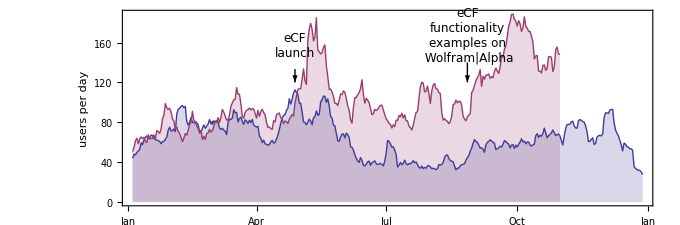

The top queries at Wolfram|Alpha that fall into the eCF domain belong to the following functionalities:

representations of concrete functions through continued fractions

theorems that apply to numbers and certain classes of continued fractions

Concretely, the most-asked questions are:

handwritten style continued fraction theorems that hold for almost all real numbers

Jacobi-Perron algorithm

Gauss-Kuzmin theorem

Euler-Minding formula

Seidel’s multiplication theorem

continued fraction theorems that hold for regular continued fractions

Schmidt’s regular chain expansion

continued fraction identities for pi

Rogers-Ramanujan continued fraction

continued fractions for 2F1

The handwritten form is a Wolfram|Alpha feature that allows users to see any result page in handwritten form. Interestingly, the theorems, which typically contain English sentences, are much more often requested in handwritten form than identities.

## Successes, Problems, and Lessons Learned

We demonstrated how a future digital mathematical library might look within a natural language processing and technical computation system.

The prototype was implemented in Wolfram|Alpha and is now used by thousands of unique users every month.

A detailed tagging system more specific than MSC 2010 is a mandatory tool for a semantic digital mathematical library because it allows us to tag individual theorems by proper mathematical phrases. Ideally, this would be a full mathematical ontology, but a wordnet-like construction is a very useful first step. Due to the size and complexity of such a system, it would have to be developed by the mathematics community at large.

In our project, we used a purely manual approach in the sense that humans read the papers and books and retyped theorems. Identities were retyped, checked, and corrected if necessary. This was a labor-intensive process, but suitable for a prototype implementation of a small field of mathematics. To scale up this approach, software tools from PDF extraction to machine learning of theorem recognition are needed to automate some steps carried out manually within the eCF project.

Implementing the prototype library in Wolfram|Alpha had the benefit of allowing access to the content using natural language. This is a nice feature, but does require a certain amount of skilled labor.

While largely developed in the nineteenth century, and mostly finished in the first half of the twentieth century, the theory of continued fraction spans many domains of mathematics from number theory to measure theory to advanced real and complex analysis. None of the project participants were experts in the theory of continued fractions, so getting familiar with the involved mathematics was sometimes time-consuming. Any digital mathematics library follow-up project should involve experts in the relevant field of mathematics.

Accumulating certain types of information, unifying them, and filling in missing pieces were the most appreciated and most used features of our library. In the eCF project, we did this for continued fraction representations for all elementary and special functions as well as for the most important properties of the Rogers-Ramanujan continued fraction.

Building fully semantic and truly computational representations of theorems is nontrivial. For a subset of the theorems from the eCF project, we created such computational representations. Once created, they were quite powerful and allowed us to decide if a theorem applied to a given mathematical expression. However, implementing the mathematical structures needed to describe theorems—constructive sets, membership tests of abstract sets, labels of objects versus the objects on their own, and so on—had a large initial overhead. In fact, ovherhead was greater than we initially estimated. As a result, we cannot answer all of the queries that we initially wanted to answer through computational deduction inside the eCF project. However, our implementation did answer some queries that we thought were not possible to answer.

In the process of building our prototype library, we had contact with various mathematicians working with continued fraction-related scientists. As a result we were able to initiate follow-up collaborations. We expect some of these projects to result in further additions to our prototype implementation that eventually cover continued fraction classes exhaustively.

## Appendix

For the convenience of the reader, this link contains screenshots of the result pages mentioned above in sample queries:
http://www.wolframfoundation.org/programs/FinalReport_Screenshots.pdf

### Definitions and concepts related to continued fractions

### Mathematical Identities for continued fractions

### Mathematical Identities for the Roger-Ramanujan continued fraction

### Theorems, conjectures, and corollaries

### Algorithms

### References